## Core parameters

```mathematica
α=0.8;β=2;γ=.;u=0;
q1=2;q2=2.5;q3=3;
p[γ_,y_,q_]:=(1-γ)q/(q1+q2+q3)+α γ (y^β/(y^β+(1-y)^β));
```

```mathematica
cols=ColorData[97,"ColorList"]⟦{2,1,3}⟧
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

## Dynamic γ

```mathematica
G=0.4;ginit=0.4;
sampleinits={{0.7,0.1},{0.1,0.7},{0.2,0.1}};
```

```mathematica
dy1[y1_,y2_,γ_]:=y1((p[γ,y1,q1] q1-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
dy2[y1_,y2_,γ_]:=y2 ((p[γ,y2,q2] q2-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
```

```mathematica
sol[{y1init_,y2init_},Gon_]:=NDSolve[{y1'[t]==dy1[y1[t],y2[t],g[t]],y2'[t]==dy2[y1[t],y2[t],g[t]],(*g evolves according to dg*)g'[t]==If[Gon==True,If[Sign[dy1[y1[t],y2[t],g[t]]]==0,0, -1  Sign[dy1[y1[t],y2[t],g[t]]] G  g[t] (1-g[t])],0],(*initial conditions*)y1[0]==y1init,y2[0]==y2init,g[0]==ginit},{y1,y2,g},{t,0,100}];
```

```mathematica
inits={};
Table[If[i+j<1,AppendTo[inits,{i,j}]],{i,0.1,1,0.1},{j,0.1,1,0.1}];
```

```mathematica
trajectoriesoff=Table[Table[Evaluate[{y1[t],1-y1[t]-y2[t],y2[t]}/.sol[inits[[j]],False]⟦1⟧],{t,0,100,0.05}],{j,1,Length[inits],1}];
trajectorieson=Table[Table[Evaluate[{y1[t],1-y1[t]-y2[t],y2[t]}/.sol[inits[[j]],True]⟦1⟧],{t,0,100,0.05}],{j,1,Length[inits],1}];
```

```mathematica
tolerance=0.01;
fixcolours[traj_]:=Table[
If[
AllTrue[Thread[Abs[Chop[Last[traj⟦i⟧]]-{1,0,0}]<tolerance],TrueQ],cols⟦1⟧,
If[AllTrue[Thread[Abs[Chop[Last[traj⟦i⟧]]-{0,1,0}]<tolerance],TrueQ],cols⟦3⟧,
If[AllTrue[Thread[Abs[Chop[Last[traj⟦i⟧]]-{0,0,1}]<tolerance],TrueQ],cols⟦2⟧,Gray]]]
,{i,1,Length[traj],1}];
```

```mathematica
coloursoff=fixcolours[trajectoriesoff];
colourson=fixcolours[trajectorieson];
```

```mathematica
(*(*Plot y1 and y2 together*)Table[Plot[Evaluate[{y1[t],1-y1[t]-y2[t],y2[t]}/.sol[inits[[j]]]],{t,0,100},PlotStyle->Automatic],{j,1,Length[inits],1}]//Show
*)
ternploff=TernaryListPlot[trajectoriesoff,Joined->True,PlotRange->All,FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧,PlotStyle->coloursoff];
ternplon=TernaryListPlot[trajectorieson,Joined->True,PlotRange->All,FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧,PlotStyle->colourson];
```

```mathematica
initstopl=Table[{{sampleinits⟦i,1⟧,1-sampleinits⟦i,1⟧-sampleinits⟦i,2⟧,sampleinits⟦i,2⟧}},{i,1,Length[sampleinits]}]
```

{{{0.7,0.2,0.1}},{{0.1,0.2,0.7}},{{0.2,0.7,0.1}}}

```mathematica
initsplotted=TernaryListPlot[initstopl,Joined->False,PlotRange->All,FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧,PlotMarkers->Automatic,PlotStyle->Black]
```

-Graphics-

```mathematica
goff=Show[ternploff,initsplotted,
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]];
```

```mathematica
gon=Show[ternplon,initsplotted,
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]];
```

```mathematica
GraphicsRow[{goff,gon}]
```

-Graphics-

```mathematica
gon
```

-Graphics-

```mathematica
Table[Evaluate[{y1[t],y2[t],1-y1[t]-y2[t],g[t],Sign[dy1[y1[t],y2[t],g[t]]]}/.sol[{0.33,0.33},True]],{t,0,100}]
```

{{{0.33,0.33,0.34,0.4,-1}},{{0.243689,0.306169,0.450142,0.498634,-1}},{{0.128374,0.199772,0.671853,0.597374,-1}},{{0.0326383,0.0576818,0.90968,0.688804,-1}},{{0.00514941,0.00988133,0.984969,0.767551,-1}},{{0.000668715,0.00136233,0.997969,0.831253,-1}},{{0.0000778812,0.000165622,0.999756,0.880222,-1}},{{8.41502×10^-6,0.0000184444,0.999973,0.91641,-1}},{{8.60926×10^-7,1.92713×10^-6,0.999997,0.94238,-1}},{{8.52112×10^-8,1.93439×10^-7,1.,0.960628,-1}},{{8.22362×10^-9,1.88474×10^-8,1.,0.973261,-1}},{{8.00538×10^-10,1.8435×10^-9,1.,0.981917,-1}},{{1.02431×10^-48,1.26593×10^-12,1.,0.987707,-1}},{{9.72327×10^-50,1.20472×10^-13,1.,0.991726,-1}},{{9.92872×10^-51,1.2329×10^-14,1.,0.994439,-1}},{{1.26173×10^-49,1.54142×10^-13,1.,0.996265,-1}},{{-2.49837×10^-78,-1.01511×10^-16,1.,0.996688,1}},{{-2.20717×10^-79,-8.98008×10^-18,1.,0.995067,1}},{{-2.8474×10^-80,-1.15922×10^-18,1.,0.992659,1}},{{-1.73977×10^-82,-8.04933×10^-21,1.,0.989088,1}},{{1.23048×10^-96,-9.57396×10^-23,1.,0.992548,-1}},{{1.48355×10^-97,-1.15402×10^-23,1.,0.994992,-1}},{{8.08966×10^-97,-6.22363×10^-23,1.,0.996638,-1}},{{1.76144×10^-133,9.11292×10^-26,1.,0.997725,-1}},{{1.53514×10^-134,7.94747×10^-27,1.,0.998474,-1}},{{2.02531×10^-136,1.06322×10^-28,1.,0.998977,-1}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}},{{0.,1.385×10^-30,1.,0.999009,0}}}

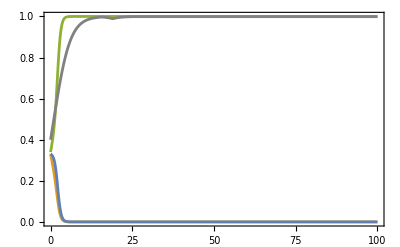

```mathematica
Plot[Evaluate[{y1[t],y2[t],1-y1[t]-y2[t],g[t]}/.sol[{0.33,0.33},True]],{t,0,100},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]]]
```

General::munfl: 1.01081×10^-298 2.13163×10^-14 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.43538×10^-308 1.70097×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

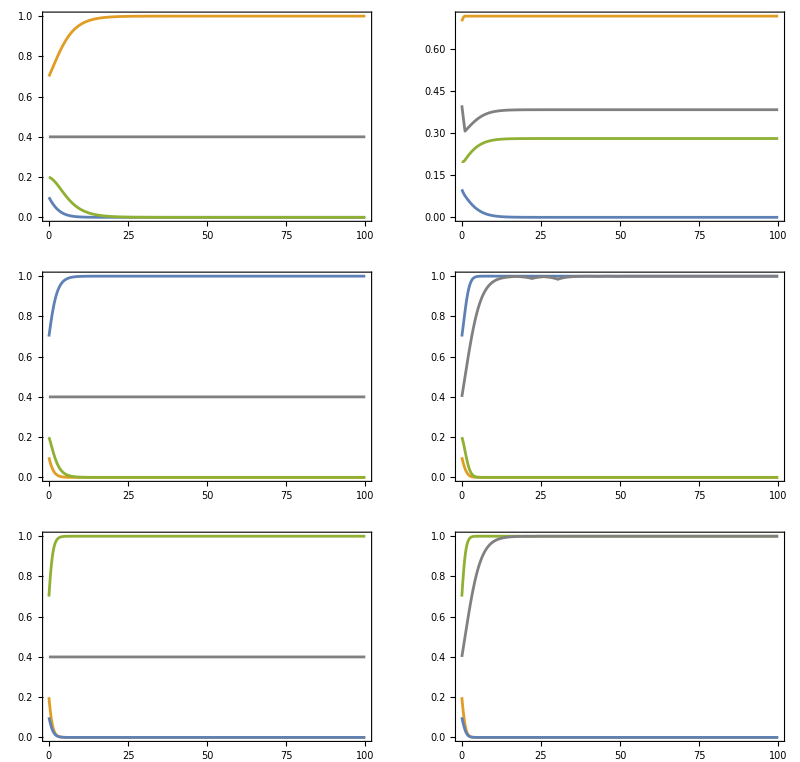

```mathematica
Table[{Plot[Evaluate[{y1[t],y2[t],1-y1[t]-y2[t],g[t]}/.sol[sampleinits⟦i⟧,False]],{t,0,100},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]]],
Plot[Evaluate[{y1[t],y2[t],1-y1[t]-y2[t],g[t]}/.sol[sampleinits⟦i⟧,True]],{t,0,100},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]]]},{i,1,3,1}]//GraphicsGrid
```